Rozwiązywanie równań różniczkowych metodą Eulera oraz zmodyfikowaną metodą Eulera.
Monika Kunkowska, 246531

Metoda Eulera:

Metoda Eulera należy do grupy metod numerycznych służących do iteracyjnego rozwiązywania równań różniczkowych. Opiera się na interpretacji geometrycznej równania różniczkowego. Swoją nazwę zawdziecza szwajcarskiemu matematykowi Leonhardowi Eulerowi, który sformuował ją w 1768 roku i przedstawił w swoim podręczniku pt. “Institutiones calculi differentialis” [1].

Dla równania różniczkowego postaci y' = x^2/y^2+y/x wyznaczyłam wartości początkowe x0 oraz y0 oraz wielkości poszczególnych kroków h1, h2 oraz h3. Użyłam trzech różnych wielkości kroków w celu sprawdzenia zależności między wielkością kroku a jakością otrzymanego przybliżenia.  Ponieważ z treści zadania  0<x<ⅇ^(1/3) użyłam zmiennej granicax w celu ograniczenia przedziału.

```mathematica
f[x_,y_]:=y/x-x^2/y^2;
x0 :=1
y0:=1
h1=0.05 
h2 = 0.1
h3 = 0.2
granicax = CubeRoot[E]
```

0.05

0.1

0.2

ⅇ^(1/3)

Następnie użyłam wbudowanej funkcji DSolve[] do rozwiązania równania różniczkowego y' = x^2/y^2+y/x o wartości początkowej y(1)=1. Funkcją Plot[] wyznaczyłam wykres funkcji, którego w dalszej części projektu używam do porównania otrzymanych metodą Eulera przybliżeń.

```mathematica
base=DSolve[{f[x,y[x]]==y'[x],y[x0]==y0},y,x]
basePlot=Plot[Evaluate[y[x]/.base],{x,x0,granicax}]
```

DSolve::dvnoarg: The function y appears with no arguments.

DSolve[{-x^2/y[x]^2+y[x]/x==(-x^2/y^2+y/x)[x],y[1]==1},y,x]

ReplaceAll::reps: {DSolve[{-x^2/y[«1»]^2+y[x]/x==(-x^2/y^2+y/x)[x],y[1]==1},y,x]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DSolve::dsvar: 1.00001 cannot be used as a variable.

ReplaceAll::reps: {DSolve[{-1.00002/y[«1»]^2+0.999992 y[1.00001]==(-1.00002/y^2+0.999992 y)[1.00001],y[1]==1},y,1.00001]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DSolve::dsvar: 1.00001 cannot be used as a variable.

ReplaceAll::reps: {DSolve[{-1.00002/y[«1»]^2+0.999992 y[1.00001]==(-1.00002/y^2+0.999992 y)[1.00001],y[1.]==1.},y,1.00001]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

DSolve::dsvar: 1.00808 cannot be used as a variable.

General::stop: Further output of DSolve::dsvar will be suppressed during this calculation.

-Graphics-

W pierwszej kolejności użyłam kroku o wielkości h=0.05 oraz wartości początkowych x0=1 oraz y0=1. Napisałam pętlę, która przy każdej iteracji dopisuje do listy list{} kolejną parę wartości. Wartości są wyznaczane za pomocą wzoru                           x0
y (x0 + h) = y x0 - h (y --)
                         x0 
Zmienna euler1 przechowuje wykres funkcji dla otrzymanej listy punktów. Otrzymany wykres przedstawia aproksymację metodą Eulera (kolor czerwony) oraz właściwy kształt wykresu funkcji otrzymany dzięki użyciu funkcji DSolve[] (kolor niebieski).

Na koniec czyszczę z pamięci programu zmienne list, x0 oraz y0, gdyż będą one używane ponownie w dalszych obliczeniach.

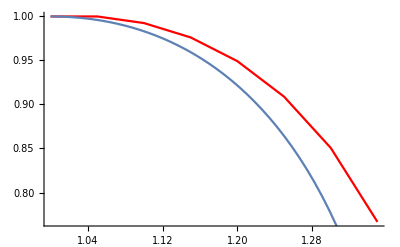

```mathematica
list={{x0,y0}};
x0 = 1;
y0 =1;
For[i=1,i≤(granicax-1)/h1,i++,
x1=x0+h1;
y1=y0+h1*f[x0,y0];
AppendTo[list, {x1,y1}];
x0=x1;
y0=y1;
]
euler1=ListPlot[list, Joined->True,PlotStyle->{RGBColor[1,0,0]}];
Show[euler1,basePlot]
Clear[list, x0, y0]
```

Tą samą operację co powyżej wykonuję dla kroku h=0.1, a następnie h=0.2. Spodziewam się tu mniej dokładnych wyników, gdyż wraz ze zwiększeniem kroku zmniejszy się ilość iteracji pętli. Zgodnie z oczekiwaniami jakość przybliżenia znacznie się pogorszyła przy h=0.1, a przy h=0.2 na tak wąskim przedziale ciężko jest cokolwiek odczytać z wykresu, gdyż pętla wykonała się zaledwie raz.

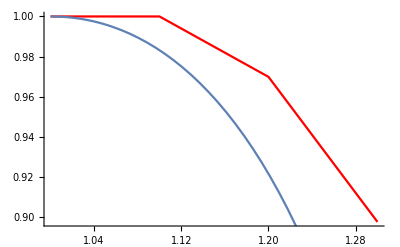

```mathematica
list={{x0,y0}};
x0 = 1;
y0 =1;
For[i=1,i≤(granicax-1)/h2,i++,
x1=x0+h2;
y1=y0+h2*f[x0,y0];
AppendTo[list, {x1,y1}];
x0=x1;
y0=y1;
]
euler2=ListPlot[list, Joined->True,PlotStyle->{RGBColor[1,0,0]}];
Show[euler2,basePlot]
Clear[list, x0, y0]
```

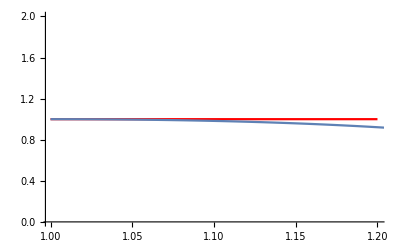

```mathematica
list={{x0,y0}};
x0 = 1;
y0 =1;
For[i=1,i≤(granicax-1)/h3,i++,
x1=x0+h3;
y1=y0+h3*f[x0,y0];
AppendTo[list, {x1,y1}];
x0=x1;
y0=y1;
]
euler3=ListPlot[list, Joined->True,PlotStyle->{RGBColor[1,0,0]}];
Show[euler3,basePlot]
Clear[list, x0, y0]
```

Modyfikowana metoda Eulera:

Modyfikowana metoda Eulera jest przekształceniem metody Eulera. Różni się tym, że zamiast szacować wartość y w punkcie x+h znajduje punkt pomiędzy x a x+h [2].
Zaimplemenowałam modyfikowaną metodę Eulera dla kolejnych kroków, rozpoczynając od h=0.05:

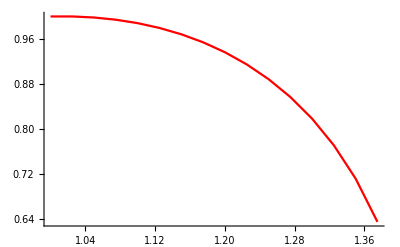

```mathematica
list={{x0,y0}};
x0 = 1;
y0 =1;
For[i=1,i≤(granicax-1)/h1*2,i++,
x1=x0+h1/2;
y1=y0+h1/2*f[x0,y0];
AppendTo[list, {x1,y1}];
x0=x1;
y0=y1;
]
eulerMod1=ListPlot[list, Joined->True,PlotStyle->{RGBColor[1,0,0]}];
Show[eulerMod1,basePlot]
Clear[list, x0, y0]
```

Następnie wykonałam tą samą operację dla kroków h=0.1 oraz h=0.2:

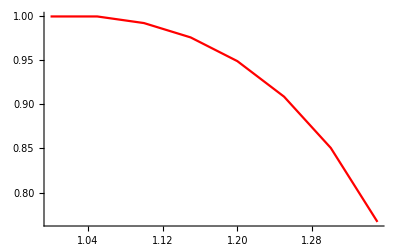

```mathematica
list={{x0,y0}};
x0 = 1;
y0 =1;
For[i=1,i≤(granicax-1)/h2*2,i++,
x1=x0+h2/2;
y1=y0+h2/2*f[x0,y0];
AppendTo[list, {x1,y1}];
x0=x1;
y0=y1;
]
eulerMod2=ListPlot[list, Joined->True,PlotStyle->{RGBColor[1,0,0]}];
Show[eulerMod2,basePlot]
Clear[list, x0, y0]
```

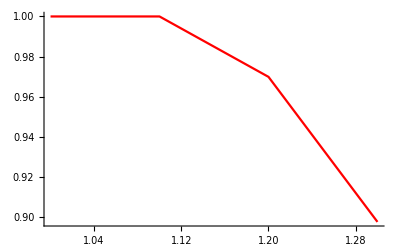

```mathematica
list={{x0,y0}};
x0 = 1;
y0 =1;
For[i=1,i≤(granicax-1)/h3*2,i++,
x1=x0+h3/2;
y1=y0+h3/2*f[x0,y0];
AppendTo[list, {x1,y1}];
x0=x1;
y0=y1;
]
eulerMod3=ListPlot[list, Joined->True,PlotStyle->{RGBColor[1,0,0]}];
Show[eulerMod3,basePlot]
Clear[list, x0, y0]
```

Można łatwo zaobserwować, że mimo pogarszania się jakości przybliżenia z wraz ze zwiększeniem wielkości kroku modyfikowana metoda Eulera daje o wiele dokładniejsze wyniki niż prosta metoda Eulera.

```mathematica
ClearAll["Global'*"]
```

Bibliografia:
[1] Atkinson, Kendall A. (1989). An Introduction to Numerical Analysis (2nd ed.). New York: John Wiley & Sons. ISBN 978-0-471-50023-0.
[2] Butcher, John C. (2003). Numerical Methods for Ordinary Differential Equations. New York: John Wiley & Sons. ISBN 978-0-471-96758-3.